# Nuevo

## Environment Setup

```mathematica
(*---Clear Kernel and load package---*)
ClearAll["Global`*"];

(*Change path if needed to find your package*)
(*AppendTo[$Path,"Path/To/Your/Package"];*)
Needs["QMB`"];

(*---Define Publication Plot Style---*)
publishStyle={Frame->True,FrameTicksStyle->Directive[Black,Scaled[0.03]],FrameLabel->{Automatic,Automatic},BaseStyle->{FontSize->Scaled[0.03],FontFamily->"Times"},ImageSize->450,AspectRatio->1 (*Keep 1:1 aspect for complex plane*)};

(*---Global Parameters for Tests---*)
matrixSize=1000; (*n=1000 is a good balance of speed and statistics*)
scaleFactor=1/Sqrt[matrixSize]; (*Standard scaling for Circular Law*)
plotPoints=2000; (*Points for CSR plots*)
```

## Ginibre Ensembles

## Unitary Ensemble

Generating GinUE (n=1000)...

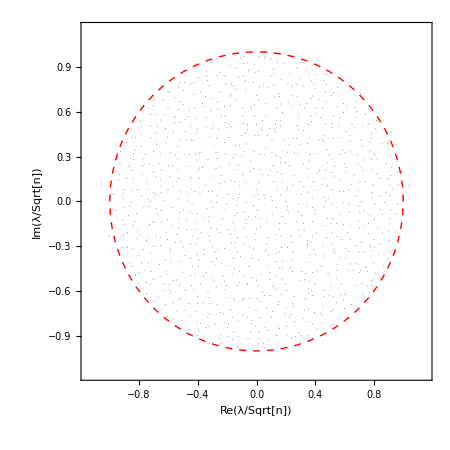

```mathematica
Print["Generating GinUE (n=1000)..."];
matGinUE=GenerateGinibreMatrix[matrixSize,Ensemble->"Unitary"];
eigsGinUE=Eigenvalues[matGinUE];

(*---Spectrum Plot---*)
ComplexListPlot[eigsGinUE*scaleFactor,PlotStyle->{Black,AbsolutePointSize[0.5]},FrameLabel->{"Re(λ/Sqrt[n])","Im(λ/Sqrt[n])"},Epilog->{Red,Dashed,Thick,Circle[{0,0},1]},Evaluate[publishStyle],PlotRange->1.15]
```

## Orthogonal Ensemble

Generating GinOE (n=1000)...

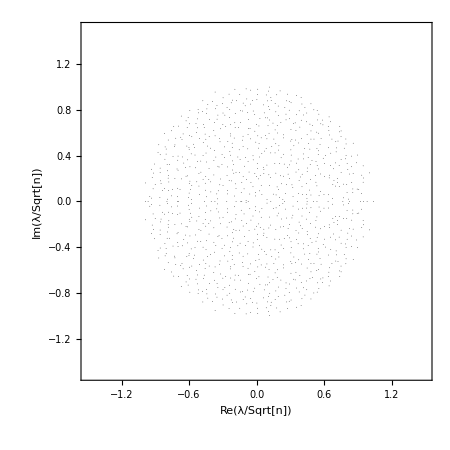

```mathematica
Print["Generating GinOE (n=1000)..."];
matGinOE=GenerateGinibreMatrix[matrixSize,Ensemble->"Orthogonal"];
eigsGinOE=Eigenvalues[matGinOE];

(*---Spectrum Plot---*)
ComplexListPlot[eigsGinOE*scaleFactor,PlotStyle->{Black,AbsolutePointSize[0.5]},FrameLabel->{"Re(λ/Sqrt[n])","Im(λ/Sqrt[n])"},Evaluate[publishStyle],PlotRange->1.5 (*Real axis extends beyond 1*)]
```

## Symplectic

Generating GinSE (n=1000 -> 2n=2000)...

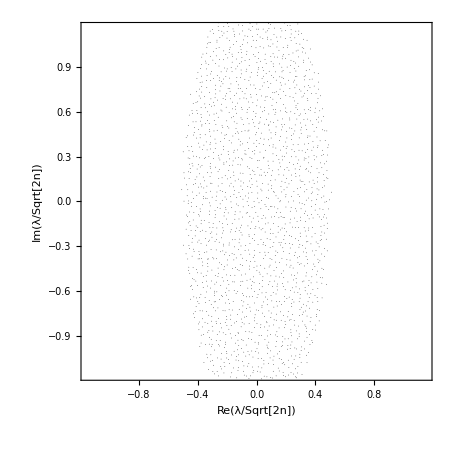

```mathematica
(* ::Subsection::2.3 Symplectic Ensemble (GinSE,β=4)*)Print["Generating GinSE (n=1000 -> 2n=2000)..."];
matGinSE=GenerateGinibreMatrix[matrixSize,Ensemble->"Symplectic"];
eigsGinSE=Eigenvalues[matGinSE];

(*---Spectrum Plot---*)
ComplexListPlot[(*GinSE scaling factor is 1/Sqrt[2*n]*)eigsGinSE/Sqrt[2*matrixSize],PlotStyle->{Black,AbsolutePointSize[0.5]},FrameLabel->{"Re(λ/Sqrt[2n])","Im(λ/Sqrt[2n])"},Evaluate[publishStyle],PlotRange->1.15]
```

## Complex spacing ratios

## Poisson

Generating Poisson spectrum (control)...

Calculating CSR for Poisson...

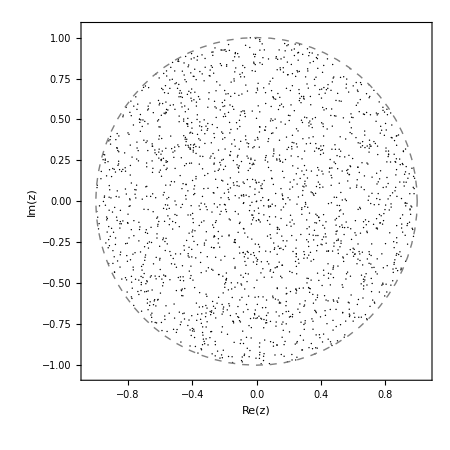

```mathematica
Print["Generating Poisson spectrum (control)..."];
eigsPoisson=RandomComplex[{-1-I,1+I},plotPoints]; (*2000 points*)

Print["Calculating CSR for Poisson..."];
csrPoisson=ComplexSpacingRatios[eigsPoisson];

(*---CSR Plot---*)
ComplexListPlot[csrPoisson,PlotStyle->{Black,AbsolutePointSize[1]},FrameLabel->{"Re(z)","Im(z)"},Epilog->{Gray,Dashed,Thick,Circle[{0,0},1]},Evaluate[publishStyle],PlotRange->1.05]
```

## Unitary

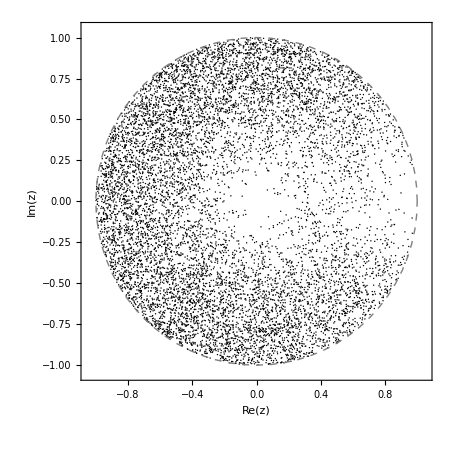

```mathematica
(*Subsample 2000 eigs for a fast CSR plot*)
eigsGinUE=
Table[
matGinUE=GenerateGinibreMatrix[matrixSize,Ensemble->"Unitary"];Eigenvalues[matGinUE]
,10];
csrGinUE=Catenate[ComplexSpacingRatios/@eigsGinUE];

(*---CSR Plot---*)
ComplexListPlot[csrGinUE,PlotStyle->{Black,AbsolutePointSize[1]},FrameLabel->{"Re(z)","Im(z)"},Epilog->{Gray,Dashed,Thick,Circle[{0,0},1]},Evaluate[publishStyle],PlotRange->1.05]
```

## Orthogonal

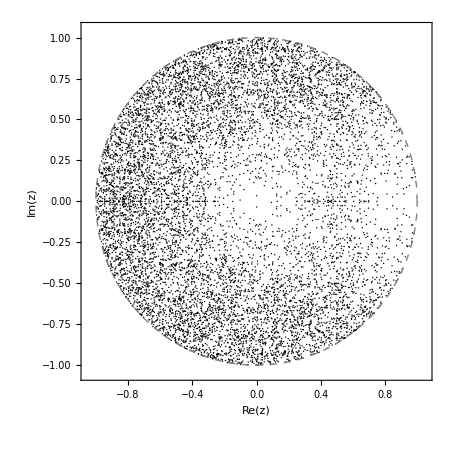

```mathematica
(*Subsample 2000 eigs for a fast CSR plot*)
eigsGinOE=
Table[
matGinOE=GenerateGinibreMatrix[matrixSize,Ensemble->"Orthogonal"];Eigenvalues[matGinOE]
,10];
csrGinOE=Catenate[ComplexSpacingRatios/@eigsGinOE];

(*---CSR Plot---*)
ComplexListPlot[csrGinOE,PlotStyle->{Black,AbsolutePointSize[1]},FrameLabel->{"Re(z)","Im(z)"},Epilog->{Gray,Dashed,Thick,Circle[{0,0},1]},Evaluate[publishStyle],PlotRange->1.05]
```

## Symplectic

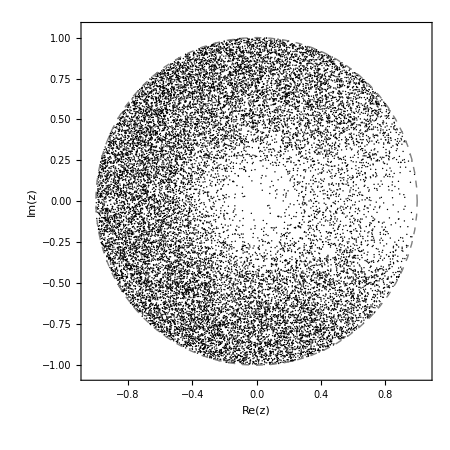

```mathematica
(*Accumulate statistics from 10 matrices*)eigsGinSE=Table[matGinSE=GenerateGinibreMatrix[matrixSize,Ensemble->"Symplectic"];
Eigenvalues[matGinSE],10];
csrGinSE=Catenate[ComplexSpacingRatios/@eigsGinSE];

(*---CSR Plot---*)
ComplexListPlot[csrGinSE,PlotStyle->{Black,AbsolutePointSize[1]}, FrameLabel->{"Re(z)","Im(z)"},Epilog->{Gray,Dashed,Thick,Circle[{0,0},1]},Evaluate[publishStyle],PlotRange->1.05]
```